# 1. DN - Računalniška orodja v matematiki

```mathematica
Dokončaj: h, d
```

#### 1. Analiza z mathematico

Točke od a do j rešite točno in tudi numerično.

a. Definirajte funkcijo .

```mathematica
f[x_]:= E^(x+3)/(100x+2)
```

b. Izračunajte definicijsko območje funkcije .

FunctionDomain[f[2],2]

```mathematica
definicijskoObmocje=Solve[100 x+2==0,x]
numeričnoObmocje=Reduce[100 x+2!=0,x,Reals]
```

{{x→-1/50}}

x<-1/50||x>-1/50

c. Izračunajte limite funkcije  na robovih definicijskega območja.

```mathematica
lim_levo=Limit[f[x],x->-0.02,Direction->"FromBelow"]
lim_desno=Limit[f[x],x->-0.02,Direction->"FromAbove"]
lim_nesoncno=Limit[f[x],x->Infinity]
lim_minus=Limit[f[x],x->-Infinity]
```

-∞

∞

∞

0

d. Izračunajte odvod funkcije .

```mathematica
f1[x_]=D[f[x], x]
```

-(100 ⅇ^(3+x))/(2+100 x)^2+ⅇ^(3+x)/(2+100 x)

e. Izračunajte lokalne ekstreme funkcije .

```mathematica
kritične_točke=Solve[f1[x]==0,x]
f2[x_]=D[f1[x],x]
drugi_odvod_v_kt=f2[x]/. kritične_točke
drugi_odvod_v_kt=f2[x]/. x->0.98
```

f. Izračunajte intervale naraščanja in padanja funkcije .

```mathematica
f1[x_]=D[f[x],x]
kritične_točke=Solve[f1[x]==0,x]
intervali_naraščanja=Reduce[f1[x]>0,x,Reals]
intervali_padanja=Reduce[f1[x]<0,x,Reals]
```

-(100 ⅇ^(3+x))/(2+100 x)^2+ⅇ^(3+x)/(2+100 x)

{{x→49/50}}

x>49/50

x<-1/50||-1/50<x<49/50

g. Narišite graf funkcije  na intervalu [-5, 5].

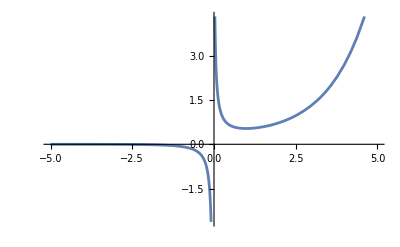

```mathematica
Plot[f[x], {x, -5, 5}]
```

h. Določite zalogo vrednosti funkcije .

i. Izračunajte nedoločeni integral funkcije .

```mathematica
nedoločen_integral=Integrate[f[x],x]
```

1/100 ⅇ^(149/50) ExpIntegralEi[1/50+x]

j. Na 3 decimalke natančno izračunajte volumen vrtenine , ki jo dobimo, če graf funkcije  zavrtimo okoli  osi an intervalu [0.5, 2]. Vrtenino tudi narišite.

```mathematica
volumen=Pi*Integrate[(f[x])^2,{x,0.5,2}]
numerični_volumen=N[volumen,3]numerični_volumen=N[volumen,3]
graf=RevolutionPlot3D[f[x],{x,0.5,2},RevolutionAxis->"X"]
```

1.66479

1.66479

-Graphics3D-

#### 2. Splošno o mathematici

a. Pobrišite vrednost vseh spremenljivk, ki ste jih uporabili v prejšnji nalogi.

```mathematica
ClearAll["Global`*"]
```

b. Definirajte funkcijo  in izračunajte njeno vrednost v vseh celih številih med 1 in 100.

```mathematica
g[x_]:= (1+ x^2.1 )/ (3+x)
vrednosti=Table[g[x],{x,1,100}]
```

{0.5,1.05742,1.84085,2.76845,3.79568,4.89604,6.05259,7.25393,8.49202,9.76096,11.0563,12.3747,13.7134,15.0702,16.4433,17.8313,19.2328,20.6469,22.0727,23.5093,24.956,26.4123,27.8776,29.3514,30.8333,32.3228,33.8198,35.3238,36.8345,38.3516,39.875,41.4044,42.9396,44.4803,46.0265,47.5778,49.1343,50.6956,52.2618,53.8326,55.4079,56.9876,58.5716,60.1598,61.7521,63.3483,64.9485,66.5525,68.1602,69.7716,71.3865,73.005,74.6269,76.2521,77.8807,79.5125,81.1475,82.7856,84.4268,86.0711,87.7183,89.3684,91.0214,92.6772,94.3359,95.9972,97.6613,99.3281,100.997,102.669,104.344,106.021,107.7,109.382,111.067,112.754,114.443,116.134,117.828,119.524,121.222,122.923,124.625,126.33,128.037,129.746,131.457,133.171,134.886,136.603,138.322,140.044,141.767,143.492,145.219,146.948,148.679,150.412,152.146,153.883}

c.  Iz seznama dobljenega v nalogi b. izberite zgolj tiste vrednosti, ki imajo na mestu enic praštevilo. Pomagajte si s _?PrimeQ in MemberQ.

```mathematica
zadnjaPraštevil0=Select[vrednosti,PrimeQ[IntegerDigits[Round[10*FractionalPart[#]]][[-1]]]&]
```

{0.5,7.25393,8.49202,13.7134,19.2328,23.5093,32.3228,35.3238,44.4803,50.6956,52.2618,60.1598,63.3483,68.1602,76.2521,79.5125,87.7183,92.6772,94.3359,97.6613,99.3281,102.669,104.344,107.7,119.524,121.222,126.33,129.746,131.457,133.171,138.322,143.492,145.219,148.679}

d. Definirajte anonimno funkcijo, ki kvadrira število in mu prišteje 1 in jo uporabite na zgoraj dobljenem seznamu.

```mathematica
anonimnaFunkcija=#^2+1&
rezultati=anonimnaFunkcija/@zadnjaPraštevil0
```

#1^2+1&

{1.25,53.6195,73.1144,189.057,370.902,553.686,1045.77,1248.77,1979.5,2571.05,2732.29,3620.2,4014.01,4646.82,5815.39,6323.24,7695.49,8590.07,8900.26,9538.73,9867.06,10542.,10888.6,11600.4,14287.,14695.8,15960.3,16835.1,17282.,17735.4,19134.1,20591.,21089.6,22106.5}

e. Seznam iz prejšnje naloge zaokrožite navzdol in seštejte vsa tista števila, ki so deliva s 3.

```mathematica
zaokroženiRezultati=Floor/@rezultati
vsotaDeljivihS3=Total[Select[zaokroženiRezultati,Mod[#,3]==0&]]
```

{1,53,73,189,370,553,1045,1248,1979,2571,2732,3620,4014,4646,5815,6323,7695,8590,8900,9538,9867,10542,10888,11600,14286,14695,15960,16835,17282,17735,19134,20590,21089,22106}

85506

#### 3. Prepisovalna pravila

```mathematica
Clear[x, y, izraz]
izraz = x^2 + 2x + 1
```

a. Definirajte prepisovalno pravilo, ki  v izrazu vse pojavitve x zamenja z y + 1.

```mathematica
Clear[x] 
x^2 + 2x + 1 /. {x -> (y+1)}
```

1+2 (1+y)+(1+y)^2

b. Z uporabo prepisovalnih pravil izračunajte vrednost izraza za  x = 2

```mathematica
x^2 + 2x + 1 /. {x -> 2}
```

9

c. Definirajte funkcija  in s pomočjo prepisovalnih pravil zamenjajte vse pojavitve  v

```mathematica
f[x_]:= x^5 - 4*x^3 + x^2 + 3*x - 2
```

```mathematica
pravilo = {x_^n_.:>2 n x^(n-1)}
```

```mathematica
-2+3 x+x^2-4 x^3+x^5/.{x_^n_.:>2 n x^(n-1)}
```

2

d. Prepisovalno pravilo iz naloge c uporabite na funkciji ,  kolikokrat gre.

```mathematica
g[x_]:= x^2025
g[x]/. {x_^n_.:>2 n x^(n-1)}
```

4050 x^2024

e. Definiraj prepisovalna pravila, s pomočjo katerih lahko izračunate poljuben člen fibonaccijevega zaporedja, z začetkom `Fib[10]`

```mathematica
Fib[0]=0
Fib[1]=1
Fib[n_]:=Fib[n]=Fib[n-1]+Fib[n-2]
Fib[10]
```

0

1

55